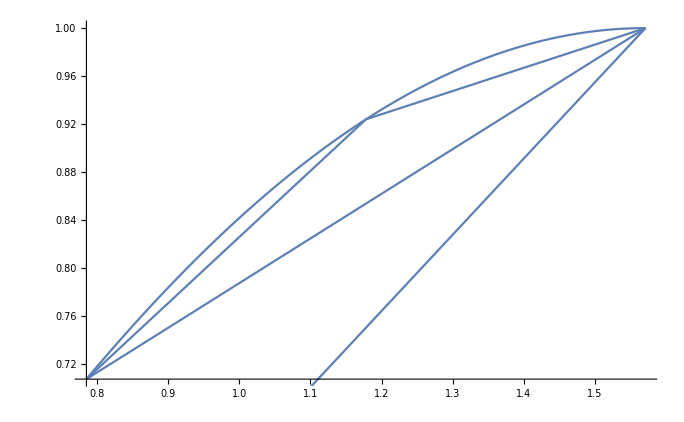

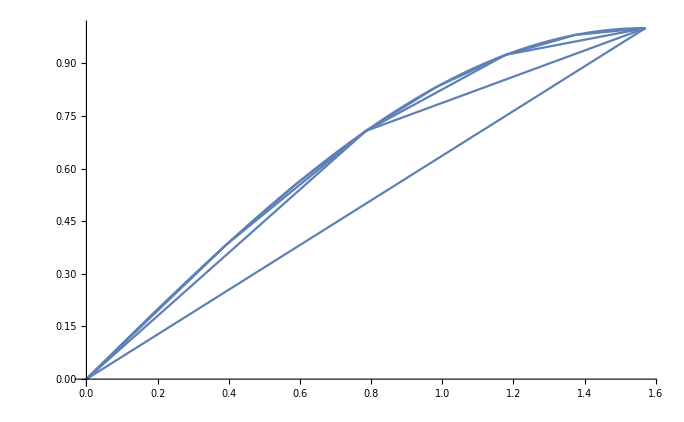

```mathematica
PL01=Plot[Sin[x],{x,0,π/2}];
PL02=Plot[x/(π/2),{x,0,π/2}];
PL03=ListPlot[Table[{x,Sin[x]},{x,0,π/2,π/16}],Joined->True];
PL04=ListPlot[Table[{x,Sin[x]},{x,0,π/2,π/8}],Joined->True];
PL05=ListPlot[Table[{x,Sin[x]},{x,0,π/2,π/4}],Joined->True];

PA01=Plot[Sin[x],{x,π/4,π/2}];
PA02=Plot[x/(π/2),{x,π/4,π/2}];
PA03=ListPlot[Table[{x,Sin[x]},{x,π/4,π/2,π/4}],Joined->True];
PA04=ListPlot[Table[{x,Sin[x]},{x,π/4,π/2,π/8}],Joined->True];

Show[PA01,PA02,PA03,PA04]
Show[PL01,PL02,PL03,PL04,PL05]
```